## Funciones

```mathematica
(* Reglas como Subscript[regla, estados, vecinos] *)
CaArray[ca_Subscript,s_,t_]:=CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t]

MakeGraph[ca_Subscript,spaceSize_]:=Module[{inits},
  inits=Tuples[Range[0,ca[[2]]-1],spaceSize];
  Graph[
   Map[FromDigits[#[[1]],ca[[2]]]->FromDigits[#[[2]],ca[[2]]] &,(CaArray[ca,#,1] & /@ inits)],
   VertexLabels->Automatic]
  ]
```

```mathematica
(* Grafo cuotientado por rotaciones: cada nodo es una clase de rotaciones ciclicas, representada por su rotacion minima *)
RotClass[state_List]:=First[Sort[NestList[RotateLeft,state,Length[state]-1]]]

MakeGraphRot[ca_Subscript,spaceSize_]:=Module[{classes},
  classes=DeleteDuplicates[RotClass /@ Tuples[Range[0,ca[[2]]-1],spaceSize]];
  Graph[(FromDigits[RotClass[#[[1]]],ca[[2]]]->FromDigits[RotClass[#[[2]]],ca[[2]]] &) /@ (CaArray[ca,#,1] &) /@ classes,
   VertexLabels->Automatic]
  ]
```

```mathematica
(* GPU: la RTX 5080 debe declararse como sm_120 (Wolfram 15 la detecta mal como sm_12) *)
cudaSession=StartExternalSession["CUDA"];

(* Un hilo por configuracion: calcula el indice de su sucesor (misma numeracion que MakeGraph) *)
succKernel=ExternalEvaluate[cudaSession,ExternalOperation["Function",
   Function[{Typed[out,"CArray"::["Integer32"]],Typed[tab,"CArray"::["Integer32"]],Typed[pw,"CArray"::["Integer64"]],
     Typed[k,"MachineInteger"],Typed[r,"MachineInteger"],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"]},
    Module[{id,new,v,cell,dig},
     id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
     If[id<total,
      new=0;
      Do[
       v=0;
       Do[
        cell=Mod[i+d,n];
        dig=Mod[Quotient[id,FromRawPointer[pw,cell]],k];
        v=v*k+dig,{d,-r,r}];
       new=new*k+FromRawPointer[tab,v],{i,0,n-1}];
      ToRawPointer[out,id,Cast[new,"Integer32","CCast"]]];
     ]],
   "CUDAArchitecture"->"sm_120"]];
```

```mathematica
(* Arreglo de sucesores (0-indexado) como NumericArray Integer32; n = numero de celulas.
   Sin temporales de 64 bits: los ceros se arman duplicando con Join y se descarga con NumericArray[out] sin tipo *)
ZerosInt32[total_Integer]:=Module[{z=NumericArray[ConstantArray[0,Min[total,2^20]],"Integer32"]},
  While[Length[z]<total,z=Join[z,z]]; z]

SuccessorArrayGPU[ca_Subscript,n_Integer]:=Module[{k=ca[[2]],m=ca[[3]],total,tab,pw,out},
  total=k^n;
  tab=GPUArray[NumericArray[Reverse[IntegerDigits[ca[[1]],k,k^m]],"Integer32"]];
  pw=GPUArray[NumericArray[k^Range[n-1,0,-1],"Integer64"]];
  out=GPUArray[ZerosInt32[total]];
  succKernel[out,tab,pw,k,(m-1)/2,n,total];
  NumericArray[out]
  ]
```

```mathematica
(* Histograma de ciclos {{longitud, numero de ciclos}, ...} de un grafo funcional (CPU compilado).
   Memoria: 4 bytes por configuracion, valido hasta 2^31 configuraciones.
   stamp (32 bits): 0 = sin visitar; el recorrido s se marca con s - 2^31 - 1 (rango [-2^31, -1]).
   Longitudes <= 2^20 se cuentan en un arreglo; las mayores (a lo mas n/2^20 ciclos) en una lista aparte. *)
cycleHistogramC=FunctionCompile[
   Function[{Typed[succ,"NumericArray"::["Integer32",1]]},
    Module[{n=Length[succ],stamp,lmax=1048576,cnt,big,nb=0,w,v,len,tag,nd=0,res,j=0,bigS},
     stamp=CreateTypeInstance["CArray"::["Integer32"],n];
     Do[ToRawPointer[stamp,i0,Cast[0,"Integer32","CCast"]],{i0,0,n-1}];
     cnt=ConstantArray[0,lmax];
     big=ConstantArray[0,Quotient[n,lmax]+1];
     Do[
      If[FromRawPointer[stamp,s-1]==Cast[0,"Integer32","CCast"],
       tag=Cast[s-2147483649,"Integer32","CCast"];
       w=s;
       While[FromRawPointer[stamp,w-1]==Cast[0,"Integer32","CCast"],
        ToRawPointer[stamp,w-1,tag]; w=succ[[w]]+1];
       If[FromRawPointer[stamp,w-1]==tag,
        len=1; v=succ[[w]]+1;
        While[v!=w,len++; v=succ[[v]]+1];
        If[len<=lmax,cnt[[len]]++,nb++; big[[nb]]=len]]],
      {s,n}];
     DeleteObject[stamp];
     Do[If[cnt[[l]]>0,nd++],{l,lmax}];
     bigS=Sort[Take[big,nb]];
     Do[If[i==1||bigS[[i]]!=bigS[[i-1]],nd++],{i,nb}];
     res=ConstantArray[0,2 nd];
     Do[If[cnt[[l]]>0,res[[2 j+1]]=l; res[[2 j+2]]=cnt[[l]]; j++],{l,lmax}];
     Do[If[i==1||bigS[[i]]!=bigS[[i-1]],res[[2 j+1]]=bigS[[i]]; res[[2 j+2]]=1; j++,res[[2 j]]++],{i,nb}];
     res]]];

CycleHistogram[ca_Subscript,n_Integer]:=<|"Nodes"->ca[[2]]^n,"Cycles"->Partition[cycleHistogramC[SuccessorArrayGPU[ca,n]],2]|>
```

```mathematica
(* Un hilo por configuracion: calcula su representante (rotacion de valor minimo) *)
rotKernel=ExternalEvaluate[cudaSession,ExternalOperation["Function",
   Function[{Typed[out,"CArray"::["Integer32"]],Typed[k,"MachineInteger"],Typed[top,"MachineInteger"],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"]},
    Module[{id,x,best},
     id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
     If[id<total,
      x=0; best=0;
      x=x+id; best=best+id;
      Do[x=Mod[x,top]*k+Quotient[x,top]; If[x<best,best=x],{i,1,n-1}];
      ToRawPointer[out,id,Cast[best,"Integer32","CCast"]]];
     ]],
   "CUDAArchitecture"->"sm_120"]];

RotationClassGPU[ca_Subscript,n_Integer]:=Module[{k=ca[[2]],total,out},
  total=k^n;
  out=GPUArray[NumericArray[ConstantArray[0,total],"Integer32"]];
  rotKernel[out,k,k^(n-1),n,total];
  NumericArray[out,"Integer32"]
  ]

(* Igual que cycleHistogramC, pero recorre solo representantes: sucesor de la clase = clase del sucesor *)
cycleHistogramRotC=FunctionCompile[
   Function[{Typed[succ,"NumericArray"::["Integer32",1]],Typed[canon,"NumericArray"::["Integer32",1]]},
    Module[{n=Length[succ],stamp,nc=0,nodes=0,w,v,len,cyc,j=0,nd=0,lens,cnts},
     stamp=ConstantArray[0,n];
     Do[
      If[canon[[s]]+1==s,
       nodes++;
       If[stamp[[s]]==0,
        w=s;
        While[stamp[[w]]==0,stamp[[w]]=s; w=canon[[succ[[w]]+1]]+1];
        If[stamp[[w]]==s,
         len=1; v=canon[[succ[[w]]+1]]+1;
         While[v!=w,len++; v=canon[[succ[[v]]+1]]+1];
         stamp[[w]]=-len; nc++]]],
      {s,n}];
     cyc=ConstantArray[0,nc];
     Do[If[stamp[[s]]<0,j++; cyc[[j]]=-stamp[[s]]],{s,n}];
     cyc=Sort[cyc];
     lens=ConstantArray[0,nc]; cnts=ConstantArray[0,nc];
     Do[If[nd>0&&lens[[nd]]==cyc[[i]],cnts[[nd]]++,nd++; lens[[nd]]=cyc[[i]]; cnts[[nd]]=1],{i,nc}];
     {nodes,Transpose[{Take[lens,nd],Take[cnts,nd]}]}]]];

(* Mismo formato que CycleHistogram; "Nodes" = numero de clases de rotacion *)
CycleHistogramRot[ca_Subscript,n_Integer]:=With[{r=cycleHistogramRotC[SuccessorArrayGPU[ca,n],RotationClassGPU[ca,n]]},
  <|"Nodes"->r[[1]],"Cycles"->r[[2]]|>]
```

```mathematica
(* Momentos espectrales: m_j = fraccion de configuraciones cuyo ciclo divide a j *)
SpectralMomentsHistogram[h_Association,kmax_Integer]:=With[{L=h["Cycles"][[All,1]],c=h["Cycles"][[All,2]]},
  N[Table[Total[L*c*Boole[Divisible[j,L]]],{j,kmax}]/h["Nodes"]]]

SpectralMomentsHistogramDistance[kmax_Integer][h1_Association,h2_Association]:=
 CosineDistance[SpectralMomentsHistogram[h1,kmax],SpectralMomentsHistogram[h2,kmax]]
```

```mathematica
(* Eigenvalores = raices de la unidad de cada ciclo + ceros.
   Corridas {angulo t en [0,1), multiplicidad} en orden canonico: modulo, Re y Im descendentes *)
EigenAngleRuns[h_Association]:=Module[{c=h["Cycles"],ds,mult},
  ds=Union @@ (Divisors /@ c[[All,1]]);
  mult=AssociationMap[Function[d,Total[Select[c,Divisible[#[[1]],d] &][[All,2]]]],ds];
  SortBy[Flatten[Table[With[{m=mult[d]},{#,m} & /@ (Select[Range[0,d-1],CoprimeQ[#,d] &]/d)],{d,ds}],1],
   {Min[#[[1]],1-#[[1]]] &,Boole[#[[1]]>1/2] &}]]

(* Vector explicito {Re, Im, Re, Im, ...} (solo para espacios pequenos) *)
EigenvaluesHistogram[h_Association]:=With[{runs=EigenAngleRuns[h]},
  Join[N@Flatten[Table[ConstantArray[{Cos[2 Pi r[[1]]],Sin[2 Pi r[[1]]]},r[[2]]],{r,runs}]],
   ConstantArray[0.,2 (h["Nodes"]-Total[runs[[All,2]]])]]]

(* Distancia coseno entre vectores de eigenvalores, sin construirlos *)
EigenvaluesHistogramDistance[h1_Association,h2_Association]:=Module[{r1=EigenAngleRuns[h1],r2=EigenAngleRuns[h2],i=1,j=1,a,b,ov,dot=0.},
  a=r1[[1,2]]; b=r2[[1,2]];
  While[i<=Length[r1]&&j<=Length[r2],
   ov=Min[a,b];
   dot += ov*N[Cos[2 Pi (r1[[i,1]]-r2[[j,1]])]];
   a -= ov; b -= ov;
   If[a==0,i++; If[i<=Length[r1],a=r1[[i,2]]]];
   If[b==0,j++; If[j<=Length[r2],b=r2[[j,2]]]]];
  1-dot/Sqrt[Total[r1[[All,2]]]*Total[r2[[All,2]]]]]
```

```mathematica
GroupRelations[rels_Association,types_ : All,extra_List : {}]:=Module[{keys,edges},
  keys=If[types===All,Keys[rels],Intersection[Flatten[{types}],Keys[rels]]];
  edges=UndirectedEdge @@@ Flatten[Lookup[rels,keys,{}]];
  SortBy[Sort /@ ConnectedComponents[Graph[extra,edges]],{-Length[#] &,First}]
  ]

(* Se aplica DESPUES de agrupar: conserva solo las ECA (2 estados, 3 vecinos) y descarta los grupos vacios *)
OnlyECA[groups_List]:=DeleteCases[Cases[#,Subscript[_,2,3]] & /@ groups,{}]

ecaRules=Table[Subscript[r,2,3],{r,0,255}];
```

## Ejecución

```mathematica
ecaHist=AssociationMap[Function[n,Table[CycleHistogram[Subscript[r,2,3],n],{r,0,255}]],Range[1,25]];
ecaHistRot=AssociationMap[Function[n,Table[CycleHistogramRot[Subscript[r,2,3],n],{r,0,255}]],Range[1,25]];
Iconize[{ecaHist,ecaHistRot},"Histogramas de ciclos ECA n = 1..25 {crudo, rotaciones}"]
```

```mathematica
{ecaHist,ecaHistRot}=;
```

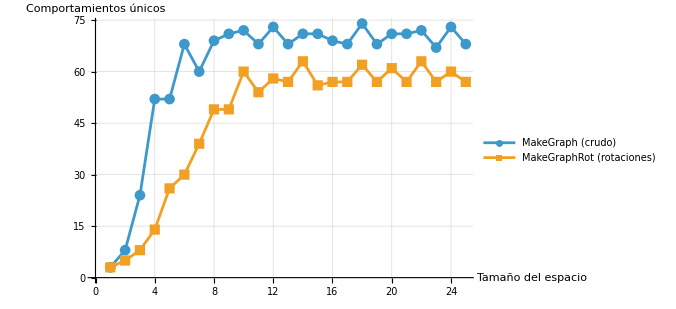

```mathematica
uniq=Length@DeleteDuplicates[#] & /@ Values[ecaHist];
uniqRot=Length@DeleteDuplicates[#] & /@ Values[ecaHistRot];
ListLinePlot[{uniq,uniqRot},DataRange->{1,25},PlotMarkers->Automatic,
 PlotLegends->{"MakeGraph (crudo)","MakeGraphRot (rotaciones)"},
 AxesLabel->{"Tamaño del espacio","Comportamientos únicos"},PlotRange->{0,Automatic},GridLines->Automatic,ImageSize->500]
```

```mathematica
relations=;
```

## Agrupación de relaciones

```mathematica
gAll=OnlyECA[gruposTodos];
gAAll=OnlyECA[gruposInvMir];
```

```mathematica
gEcahist=Subscript[#,2,3]&/@#&/@
Values[GroupBy[Thread[Range[0,255]->ecaHist[18]],Last->First]];
gEcahistRot=Subscript[#,2,3]&/@#&/@
Values[GroupBy[Thread[Range[0,255]->ecaHistRot[22]],Last->First]];
```

```mathematica
UniqueElements[{gAll,gAAll}];
```

```mathematica
Length[#]&/@{gAll,gAAll,gEcahist,gEcahistRot}
```

{81,88,74,63}

VAMOS A USA gAll. Las agrupaciones obtenidas por las reducciones de estados son validas, las vamos a considerar dentro de la misma clasificación. Ahora el momento es comparar gEcahist y gEcahistrot

```mathematica
UniqueElements[{gAll,gEcahist}];
```

```mathematica
(*Para cada grupo de "grandes":que grupos de "chicos" caen completos dentro,si lo cubren exactamente,y cuales lo cruzan parcialmente*)Descomponer[grandes_List,chicos_List]:=Table[With[{dentro=Select[chicos,SubsetQ[g,#]&]},<|"Grupo"->g,"Partes"->dentro,"NPartes"->Length[dentro],"Exacto"->Sort[Flatten[dentro]]===Sort[g],"Cruzados"->Select[chicos,IntersectingQ[g,#]&&!SubsetQ[g,#]&&!SubsetQ[#,g]&]|>],{g,grandes}];

dA=Descomponer[gAll,gEcahist];   (*gAll partido en grupos de gEcahist*)
dE=Descomponer[gEcahist,gAll];   (*gEcahist partido en grupos de gAll*)

Select[dA,#Exacto&&#NPartes>1&]   ;(*grupos de gAll hechos de varios de gEcahist*)
Select[dE,#Exacto&&#NPartes>1&]   ;(*grupos de gEcahist hechos de varios de gAll*)
Select[dA,#Cruzados=!={}&]          ;(*traslapes parciales:ninguno contiene al otro*)
```

```mathematica
Select[dA,#Exacto&&#NPartes>1&]
```

{<|Grupo→{3_(2,3),5_(2,3),17_(2,3),63_(2,3),95_(2,3),119_(2,3)},Partes→{{3_(2,3),17_(2,3),63_(2,3),119_(2,3)},{5_(2,3),95_(2,3)}},NPartes→2,Exacto→True,Cruzados→{}|>,<|Grupo→{60_(2,3),90_(2,3),102_(2,3),153_(2,3),165_(2,3),195_(2,3)},Partes→{{60_(2,3),102_(2,3),153_(2,3),195_(2,3)},{90_(2,3),165_(2,3)}},NPartes→2,Exacto→True,Cruzados→{}|>}

Aqui tenemos resultados.

```mathematica
(*Comportamientos que coinciden*)
Flatten[Intersection[gAll,gEcahist]]//Length
(*Comportamientos similiares de gAll que gEcaHist clasifica como diferentes*)
Flatten[Select[dA,#Exacto&&#NPartes>1&][[;;,"Grupo"]]]//Length
(*Comportamientos diferentes de gAll que gEcaHist clasifica como iguales*)
Flatten[Select[dE,#Exacto&&#NPartes>1&][[;;,"Grupo"]]]//Length
(*Comportamientos cruzados,es decir, diferentes comportamientos combinados de ambos*)
Flatten[Select[dA,#Cruzados=!={}&][[;;,"Grupo"]]]//Length

Flatten[Select[dE,#Cruzados=!={}&][[;;,"Grupo"]]]//Length
```

160

12

56

24

16

```mathematica
Position[gEcahist,Subscript[4,2,3]]
```

{{5,1}}

```mathematica
gAll[[47]]
gEcahist[[5]]
```

{4_(2,3),223_(2,3)}

{4_(2,3),12_(2,3),68_(2,3),207_(2,3),221_(2,3),223_(2,3)}

```mathematica
160+12+56+24
```

252

```mathematica
Select[dA,#Cruzados=!={}&]
```

{<|Grupo→{10_(2,3),12_(2,3),34_(2,3),48_(2,3),68_(2,3),80_(2,3),175_(2,3),187_(2,3),207_(2,3),221_(2,3),243_(2,3),245_(2,3)},Partes→{{10_(2,3),80_(2,3),175_(2,3),245_(2,3)},{34_(2,3),48_(2,3),187_(2,3),243_(2,3)}},NPartes→2,Exacto→False,Cruzados→{{4_(2,3),12_(2,3),68_(2,3),207_(2,3),221_(2,3),223_(2,3)}}|>,<|Grupo→{136_(2,3),160_(2,3),192_(2,3),238_(2,3),250_(2,3),252_(2,3)},Partes→{{160_(2,3),250_(2,3)}},NPartes→1,Exacto→False,Cruzados→{{128_(2,3),136_(2,3),192_(2,3),238_(2,3),252_(2,3),254_(2,3)}}|>,<|Grupo→{15_(2,3),51_(2,3),85_(2,3)},Partes→{{51_(2,3)}},NPartes→1,Exacto→False,Cruzados→{{15_(2,3),85_(2,3),170_(2,3),240_(2,3)}}|>,<|Grupo→{170_(2,3),204_(2,3),240_(2,3)},Partes→{{204_(2,3)}},NPartes→1,Exacto→False,Cruzados→{{15_(2,3),85_(2,3),170_(2,3),240_(2,3)}}|>}

### Comparación de gAll contra los histogramas de ciclos

CompararClasificaciones une en un bloque todos los grupos de ambas clasificaciones que comparten reglas, y clasifica cada bloque según cuántos grupos tiene de cada lado. Así cada regla cae en exactamente una de cuatro categorías y la suma siempre da 256.

Coinciden: un grupo de A y un grupo de B, idénticos.

A junta, B separa: un grupo de A partido en varios grupos de B.

A separa, B junta: varios grupos de A unidos en un grupo de B.

Cruzados: varios grupos de cada lado que se traslapan sin que ninguno contenga al otro.

```mathematica
(* Une grupos de ambas clasificaciones que comparten reglas; cada bloque se clasifica
   segun cuantos grupos de cada lado contiene. A = primera lista, B = segunda *)
CompararClasificaciones[gA_List,gB_List]:=Module[{nodos,aristas,comps},
  nodos=Join[Thread[{"A",Range[Length[gA]]}],Thread[{"B",Range[Length[gB]]}]];
  aristas=Flatten[Table[If[IntersectingQ[gA[[i]],gB[[j]]],{"A",i} <-> {"B",j},Nothing],
     {i,Length[gA]},{j,Length[gB]}]];
  comps=ConnectedComponents[Graph[nodos,aristas]];
  Map[Function[c,With[{a=gA[[Cases[c,{"A",i_}:>i]]],b=gB[[Cases[c,{"B",j_}:>j]]]},
      <|"Tipo"->Which[Length[a]==1&&Length[b]==1,"Coinciden",
         Length[b]>1&&Length[a]==1,"A junta, B separa",
         Length[a]>1&&Length[b]==1,"A separa, B junta",
         True,"Cruzados"],
       "Reglas"->Sort[Flatten[a]],"GruposA"->a,"GruposB"->b|>]],comps]];

bloques=CompararClasificaciones[gAll,gEcahist];
cuenta=Length@*Flatten /@ GroupBy[bloques,#Tipo &,#[[All,"Reglas"]] &]
Total[cuenta]
```

<|Cruzados→28,A separa, B junta→56,A junta, B separa→12,Coinciden→160|>

256

Conteo de las cuatro categorías para cada tamaño del espacio, sin cocientar (ecaHist) y cocientado por rotaciones (ecaHistRot), siempre contra gAll.

```mathematica
(* Agrupa las 256 ECA por histograma identico, en la notacion Subscript[r, 2, 3] *)
GruposHist[h_List]:=Map[Subscript[#,2,3] &,Values[GroupBy[Thread[Range[0,255]->h],Last->First]],{2}];

categorias={"Coinciden","A junta, B separa","A separa, B junta","Cruzados"};
etiquetas={"Coinciden","gAll junta, histograma separa","gAll separa, histograma junta","Cruzados"};

(* Numero de reglas en cada categoria al comparar gAll contra una clasificacion *)
ConteoCategorias[gB_List]:=With[{c=Length@*Flatten /@ GroupBy[CompararClasificaciones[gAll,gB],#Tipo &,#[[All,"Reglas"]] &]},
   Lookup[c,categorias,0]];

conteoRaw=Table[ConteoCategorias[GruposHist[ecaHist[n]]],{n,1,25}];
conteoRot=Table[ConteoCategorias[GruposHist[ecaHistRot[n]]],{n,1,25}];

PlotCategorias[datos_,titulo_]:=ListLinePlot[Transpose[datos],DataRange->{1,25},
   PlotMarkers->Automatic,PlotLegends->etiquetas,PlotLabel->titulo,
   AxesLabel->{"Tamaño del espacio","Reglas"},PlotRange->{0,256},GridLines->Automatic,ImageSize->500];
```

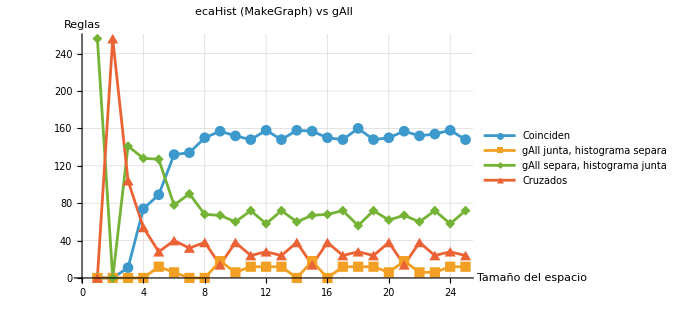

```mathematica
PlotCategorias[conteoRaw,"ecaHist (MakeGraph) vs gAll"]
```

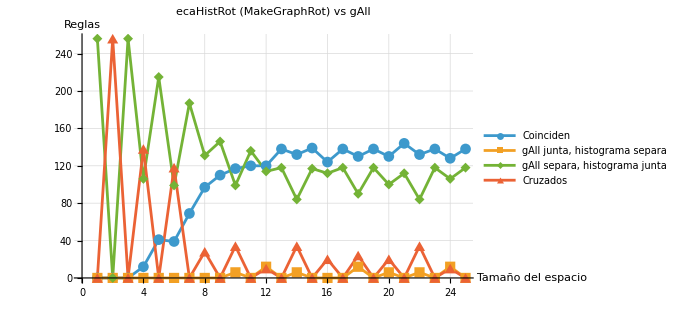

```mathematica
PlotCategorias[conteoRot,"ecaHistRot (MakeGraphRot) vs gAll"]
```

## Periodicidad en el tamaño del espacio

Resultados completos, tablas y conclusiones en resultados_periodicidad_histogramas.md (carpeta del proyecto). Esta sección guarda el código y carga los datos que se calcularon fuera del notebook. Requiere haber evaluado las secciones anteriores (ecaHist, gAll, gruposInvMirECA, CompararClasificaciones, GruposHist, ConteoCategorias, PlotCategorias).

### Datos calculados fuera del notebook

ecaHist_26_28.wl y ecaHist_31.wl: histogramas ECA con 26, 27, 28 y 31 células. hist22.wl: las 16 reglas de 2 estados y 2 vecinos, sin cocientar (1 a 31) y con rotaciones (1 a 29).

```mathematica
dirProyecto="/home/rediax/Documents/Projects/CA-Similarity-Index/";
ecaHist=Join[ecaHist,Get[dirProyecto <> "ecaHist_26_28.wl"],Get[dirProyecto <> "ecaHist_31.wl"]];
hist22=Get[dirProyecto <> "hist22.wl"];
raw22=hist22["raw"];
rot22=hist22["rot"];
Keys /@ {ecaHist,raw22,rot22}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,31},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

### Funciones auxiliares

```mathematica
(* Grafos de transicion de varias reglas con i celulas. rot = True usa MakeGraphRot *)
PlotRulesGraph[rules_List,i_Integer,rot_ : False]:=Grid[Partition[
    Table[Labeled[
      Graph[If[rot,MakeGraphRot,MakeGraph][r,i],VertexLabels->If[i<=4,Automatic,None],VertexSize->Small,ImageSize->220],
      Row[{"Regla ",r[[1]]}],Top],{r,rules}],UpTo[3]],Frame->All];

(* Una regla representativa por grupo inverse/mirror: en ECA comparten histograma (verificado n = 1..25) *)
repDe=Association[Flatten[Thread[#->First[#]] & /@ gruposInvMirECA]];
ExpandirReps[h_Association]:=Table[h[repDe[Subscript[r,2,3]]],{r,0,255}];

(* Particion por histograma para n celulas, y la misma sin las reglas lineales/afines *)
ParticionECA[n_]:=Sort[Sort /@ GruposHist[ecaHist[n]]];
linealesECA=Subscript[#,2,3] & /@ {0,60,90,102,150,170,204,240,255,195,165,153,105,85,51,15};
ParticionSinLineales[n_]:=Sort[DeleteCases[Sort /@ (Complement[#,linealesECA] & /@ ParticionECA[n]),{}]];

(* Familias de tamanos con exactamente la misma particion *)
FamiliasECA[ns_List]:=Values[GroupBy[ns,ParticionECA]];
FamiliasSinLineales[ns_List]:=Values[GroupBy[ns,ParticionSinLineales]];
```

```mathematica
FamiliasSinLineales[Join[Range[1,28],{31}]]
```

{{1},{2},{3},{4},{5},{6},{7},{8,10,14,16,20,22,26,28},{9,15,21,27},{11,13,17,19,23,25,31},{12,18,24}}

### Espacio de 2 estados y 2 vecinos

Con 2 vecinos la vecindad de la celda i es (i - 1, i), que no es simetrica. El kernel succKernel solo acepta vecindades -r..r, asi que succKernelLH recibe el rango lo..hi (m impar: -r..r; m = 2: -1..0).

```mathematica
(* Un hilo por configuracion; vecindad = celdas i+lo .. i+hi *)
succKernelLH=ExternalEvaluate[cudaSession,ExternalOperation["Function",
    Function[{Typed[out,"CArray"::["Integer32"]],Typed[tab,"CArray"::["Integer32"]],Typed[pw,"CArray"::["Integer64"]],
      Typed[k,"MachineInteger"],Typed[lo,"MachineInteger"],Typed[hi,"MachineInteger"],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"]},
     Module[{id,new,v,cell,dig},
      id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
      If[id<total,
       new=0;
       Do[
        v=0;
        Do[
         cell=Mod[i+d,n];
         dig=Mod[Quotient[id,FromRawPointer[pw,cell]],k];
         v=v*k+dig,{d,lo,hi}];
        new=new*k+FromRawPointer[tab,v],{i,0,n-1}];
       ToRawPointer[out,id,Cast[new,"Integer32","CCast"]]];
      ]],
    "CUDAArchitecture"->"sm_120"]];

SuccessorArrayGPULH[ca_Subscript,n_Integer]:=Module[{k=ca[[2]],m=ca[[3]],total,tab,pw,out},
   total=k^n;
   tab=GPUArray[NumericArray[Reverse[IntegerDigits[ca[[1]],k,k^m]],"Integer32"]];
   pw=GPUArray[NumericArray[k^Range[n-1,0,-1],"Integer64"]];
   out=GPUArray[ZerosInt32[total]];
   succKernelLH[out,tab,pw,k,-Ceiling[(m-1)/2],Floor[(m-1)/2],n,total];
   NumericArray[out]];

CycleHistogramLH[ca_Subscript,n_Integer]:=<|"Nodes"->ca[[2]]^n,"Cycles"->Partition[cycleHistogramC[SuccessorArrayGPULH[ca,n]],2]|>;
CycleHistogramRotLH[ca_Subscript,n_Integer]:=With[{r=cycleHistogramRotC[SuccessorArrayGPULH[ca,n],RotationClassGPU[ca,n]]},
   <|"Nodes"->r[[1]],"Cycles"->r[[2]]|>];
```

```mathematica
rules22=Table[Subscript[r,2,2],{r,0,15}];
gAll22=DeleteCases[Cases[#,Subscript[_,2,2]] & /@ GroupRelations[relations,All,Join[ecaRules,rules22]],{}];
Grupos22[h_List]:=Map[Subscript[#,2,2] &,Values[GroupBy[Thread[Range[0,15]->h],Last->First]],{2}];
Conteo22[gB_List]:=With[{c=Length@*Flatten /@ GroupBy[CompararClasificaciones[gAll22,gB],#Tipo &,#[[All,"Reglas"]] &]},
   Lookup[c,categorias,0]];
conteo22raw=Table[Conteo22[Grupos22[raw22[n]]],{n,1,31}];
conteo22rot=Table[Conteo22[Grupos22[rot22[n]]],{n,1,29}];
PlotCategorias22[datos_,titulo_,nmax_]:=ListLinePlot[Transpose[datos],DataRange->{1,nmax},
   PlotMarkers->Automatic,PlotLegends->etiquetas,PlotLabel->titulo,
   AxesLabel->{"Tamaño del espacio","Reglas"},PlotRange->{0,16},GridLines->Automatic,ImageSize->500];
```

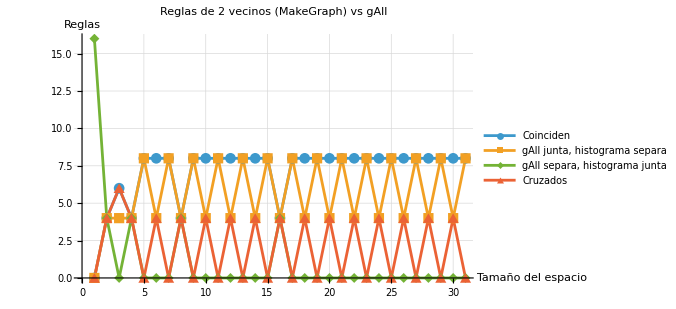

```mathematica
PlotCategorias22[conteo22raw,"Reglas de 2 vecinos (MakeGraph) vs gAll",31]
```

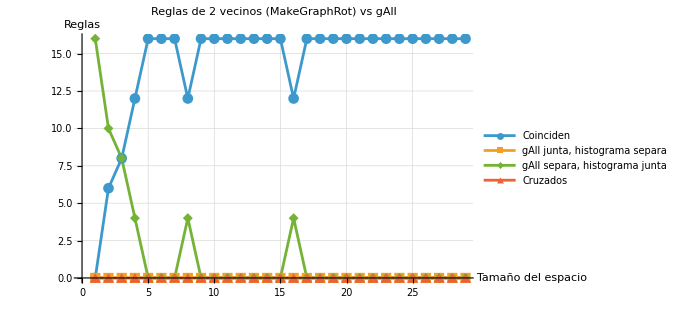

```mathematica
PlotCategorias22[conteo22rot,"Reglas de 2 vecinos (MakeGraphRot) vs gAll",29]
```

## Eigenvalores en GPU: 88 reglas, n = 1, …, 29

Clasificación de las 88 reglas representantes (una por clase de inverso + espejo) por el espectro de la matriz de adyacencia de su grafo de transición, para n = 1, …, 29 células. Es la misma metodología que canonical_form_gpu.nb: una regla por clase, un archivo de datos por tamaño, el resultado iconizado y la gráfica.

El grafo de transición es funcional, así que su espectro sale solo de los ciclos: un ciclo de longitud L aporta las L raíces L-ésimas de la unidad y cada nodo de los árboles aporta un eigenvalor 0. Por eso no se diagonaliza la matriz (2^n × 2^n): EigenSpectrum guarda el espectro exacto en forma compacta, la multiplicidad del 0 y, para cada d, la multiplicidad de las raíces primitivas d-ésimas (el número de ciclos cuya longitud es múltiplo de d). El histograma de ciclos se calcula con SuccessorArrayGPU y cycleHistogramC de la sección Funciones. Dos reglas tienen el mismo espectro si y solo si tienen el mismo histograma de ciclos.

Validación: para n = 1..6 la partición coincide con la que se obtiene agrupando por el polinomio característico exacto de la matriz de adyacencia, y para n = 1..28 coincide con la de ecaHist (256 reglas, calculada antes).

### Funciones

```mathematica
(* Espectro exacto de la matriz de adyacencia a partir del histograma de ciclos: un ciclo de longitud L aporta las L raíces L-ésimas de la unidad, así que las raíces primitivas d-ésimas tienen multiplicidad igual al número de ciclos con d | L; los árboles solo aportan el eigenvalor 0 *)
EigenSpectrum[h_Association]:=Module[{c=h["Cycles"],ds},ds=Union@@(Divisors/@c[[All,1]]);<|"Zero"->h["Nodes"]-Total[c[[All,1]]*c[[All,2]]],"Roots"->Table[{d,Total[Select[c,Divisible[#[[1]],d]&][[All,2]]]},{d,ds}]|>];
(* Una regla: histograma de ciclos en GPU + CPU compilado y su espectro *)
EigenvaluesGPU[r_Integer,n_Integer]:=Module[{h=CycleHistogram[Subscript[r,2,3],n]},<|"Rule"->r,"n"->n,"Cycles"->h["Cycles"],"Spectrum"->EigenSpectrum[h]|>];
(* Mínimo de cada clase bajo espejo e inverso (88 reglas) *)
mirrorRule[r_]:=Sum[BitGet[r,4BitGet[v,0]+2BitGet[v,1]+BitGet[v,2]]2^v,{v,0,7}];
complementRule[r_]:=Sum[(1-BitGet[r,7-v])2^v,{v,0,7}];
ecaReps=Union[Table[Min[r,mirrorRule[r],complementRule[r],mirrorRule[complementRule[r]]],{r,0,255}]];
Length[ecaReps]
```

88

### Experimento

Cada tamaño se guarda en eigenvalues_gpu_data.wl; si el archivo existe, solo se calculan los tamaños que faltan. Requiere evaluar antes la sección Funciones (sesión CUDA, SuccessorArrayGPU y cycleHistogramC).

```mathematica
nMax=29;
dataFileEig=FileNameJoin[{Quiet[Check[NotebookDirectory[],Directory[]]],"eigenvalues_gpu_data.wl"}];
eigResults=If[FileExistsQ[dataFileEig],Get[dataFileEig],<||>];
Do[If[!KeyExistsQ[eigResults,n],Module[{rows,t},t=First[AbsoluteTiming[rows=Table[EigenvaluesGPU[r,n],{r,ecaReps}]]];eigResults[n]=<|"n"->n,"Seconds"->t,"Classes"->CountDistinct[rows[[All,"Spectrum"]]],"Groups"->Values[GroupBy[rows,#["Spectrum"]&,#[[All,"Rule"]]&]],"Rules"->rows|>;Put[eigResults,dataFileEig]]],{n,1,nMax}];
Dataset[KeyTake[#,{"n","Classes","Seconds"}]&/@Values[KeySort[eigResults]]]
```

### Datos (Iconize)

```mathematica
eigData=;
```

### Gráfica

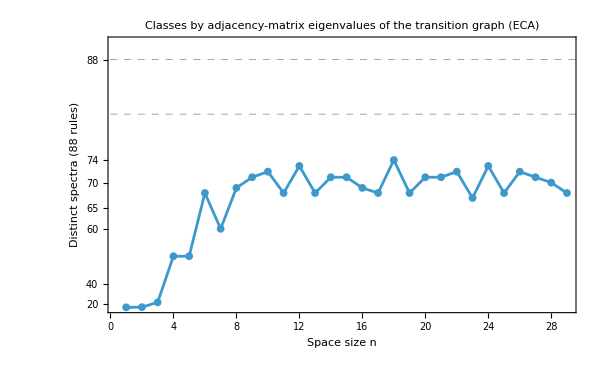

```mathematica
ptsEig={#["n"],#["Classes"]}&/@Values[KeySort[eigData]];
yScale={#^3&,CubeRoot};
ListLinePlot[ptsEig,PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct spectra (88 rules)"},FrameTicks->{{{20,40,60,65,70,74,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by adjacency-matrix eigenvalues of the transition graph (ECA)"]
```

### Resultados

Clases por n: 3, 8, 24, 52, 52, 68, 60 para n = 1..7, y entre 67 y 74 desde n = 8 (máximo 74 con n = 18, mínimo 67 con n = 23). Siempre son menos que con la forma canónica (82–85): el espectro solo ve los ciclos, no las cuencas, así que agrupa reglas con grafos no isomorfos (por ejemplo, 0 y 8). En todos los tamaños la partición por forma canónica es más fina que la del espectro.

Particiones idénticas: {8, 16}, {9, 15, 21, 27}, {10, 22, 26}, {11, 13, 17, 19, 25, 29} y {12, 24}; los demás tamaños quedan aparte. n = 29 confirma el patrón de gcd(n, 12) descrito en resultados_periodicidad_histogramas.md (queda con 11, 13, 17, 19, 25). Las excepciones vienen de las reglas lineales: 20 y 28 se separan de 8 y 16 porque no son potencias de 2, y 23 y 28 porque en ellos se juntan 60 y 90.

Combinando los 29 tamaños se obtienen 77 clases, y la mejor combinación de dos tamaños también da 77 (por ejemplo n = 27 y 28). Ningún conjunto de tamaños llega a las 88: en los 29 tamaños tienen el mismo espectro {0, 8}, {1, 19}, {2, 24, 46}, {4, 12}, {18, 126}, {36, 72}, {128, 136}, {130, 152}, {132, 140} y {162, 168}, reglas con los mismos ciclos que solo difieren en sus transitorios.

Tiempo total: 29 min en la RTX 5080 (n = 29 tarda 16 min); a diferencia de la forma canónica, el recorrido de los ciclos se hace en CPU.

## Eigenvalores del cociente por rotaciones en GPU: 88 reglas, n = 1, …, 29

Mismo experimento de eigenvalores, pero sobre el grafo cociente por rotaciones (el de MakeGraphRot): cada nodo es una clase de configuraciones bajo rotación cíclica y la arista va de [x] a [F(x)]. El cociente también es un grafo funcional, así que su espectro sale igual de su histograma de ciclos (EigenSpectrum).

En lugar de CycleHistogramRot, que recorre las 2^n configuraciones, los sucesores del cociente se calculan en GPU con los mismos kernels que canonical_form_gpu.nb: kRepMark marca los representantes (rotación mínima) y guarda su índice compacto, y kSuccQuot aplica la regla a cada representante y busca el índice de la rotación mínima del resultado. cycleHistogramC recorre solo los unos 2^n/n nodos del cociente: las 88 reglas con n = 29 tardan 33 s y todo el rango 73 s (contra 29 min sin cocientar).

Validación: para n = 1..8 la partición coincide con la que se obtiene agrupando por el polinomio característico exacto de la matriz de adyacencia del cociente, y para n = 1..25 coincide con la de ecaHistRot (256 reglas, calculada antes con CycleHistogramRot).

### Funciones

```mathematica
(* Representantes de las clases de rotación: configuraciones iguales a su rotación mínima; idx[x] guarda el índice compacto de cada representante *)
kRepMark=ExternalEvaluate[cudaSession,ExternalOperation["Function",Function[{Typed[reps,TypeSpecifier["CArray"]["Integer32"]],Typed[idx,TypeSpecifier["CArray"]["Integer32"]],Typed[cnt,TypeSpecifier["CArray"]["Integer32"]],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"]},Module[{id,x,y,m,mask,k,i},id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];If[id<total,x=Cast[id,"UnsignedInteger64","CCast"];mask=Cast[total-1,"UnsignedInteger64","CCast"];m=x;y=x;k=1;While[k<n,y=BitAnd[BitOr[BitShiftLeft[y,1],BitShiftRight[y,n-1]],mask];If[y<m,m=y];k=k+1];If[m==x,i=Compile`AtomicUpdate[cnt,0,"Plus",Cast[1,"Integer32","CCast"]];ToRawPointer[reps,i,Cast[id,"Integer32","CCast"]];ToRawPointer[idx,id,i]]];]],"CUDAArchitecture"->"sm_120"]];
(* Sucesor en el cociente: se aplica la regla ECA al representante y se busca el índice de la rotación mínima del resultado *)
kSuccQuot=ExternalEvaluate[cudaSession,ExternalOperation["Function",Function[{Typed[succ,TypeSpecifier["CArray"]["Integer32"]],Typed[reps,TypeSpecifier["CArray"]["Integer32"]],Typed[idx,TypeSpecifier["CArray"]["Integer32"]],Typed[rule,"MachineInteger"],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"],Typed[nr,"MachineInteger"]},Module[{id,x,mask,l,r,nx,a,b,c,y,m,k},id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];If[id<nr,x=Cast[FromRawPointer[reps,id],"UnsignedInteger64","CCast"];mask=Cast[total-1,"UnsignedInteger64","CCast"];l=BitAnd[BitOr[BitShiftRight[x,1],BitShiftLeft[x,n-1]],mask];r=BitAnd[BitOr[BitShiftLeft[x,1],BitShiftRight[x,n-1]],mask];nx=Cast[0,"UnsignedInteger64","CCast"];Do[If[BitAnd[BitShiftRight[rule,v],1]==1,a=If[BitAnd[v,4]!=0,l,BitXor[l,mask]];b=If[BitAnd[v,2]!=0,x,BitXor[x,mask]];c=If[BitAnd[v,1]!=0,r,BitXor[r,mask]];nx=BitOr[nx,BitAnd[BitAnd[a,b],c]]],{v,0,7}];m=nx;y=nx;k=1;While[k<n,y=BitAnd[BitOr[BitShiftLeft[y,1],BitShiftRight[y,n-1]],mask];If[y<m,m=y];k=k+1];ToRawPointer[succ,id,FromRawPointer[idx,Cast[m,"MachineInteger","CCast"]]]];]],"CUDAArchitecture"->"sm_120"]];
```

```mathematica
(* Los representantes solo dependen de n: se calculan una vez por tamaño. ZerosInt32 redondea hacia arriba la longitud, así que succ se recorta a exactamente nr entradas *)
AllocateQuotient[n_]:=Module[{total=2^n,cnt,reps,idx,nr},reps=GPUArray[ZerosInt32[total]];idx=GPUArray[ZerosInt32[total]];cnt=GPUArray[NumericArray[ConstantArray[0,8],"Integer32"]];kRepMark[reps,idx,cnt,n,total];nr=First[Normal[NumericArray[cnt]]];<|"n"->n,"N"->nr,"total"->total,"reps"->GPUArray[Take[NumericArray[reps],nr]],"idx"->idx,"succ"->GPUArray[Take[ZerosInt32[nr],nr]]|>];
(* Una regla: sucesores del cociente en GPU, histograma de ciclos en CPU compilado y su espectro *)
EigenvaluesRotGPU[r_Integer,buf_Association]:=Module[{h},kSuccQuot[buf["succ"],buf["reps"],buf["idx"],r,buf["n"],buf["total"],buf["N"],"GridDimensions"->Quotient[buf["N"]-1,256]+1,"BlockDimensions"->256];h=<|"Nodes"->buf["N"],"Cycles"->Partition[cycleHistogramC[NumericArray[buf["succ"]]],2]|>;<|"Rule"->r,"n"->buf["n"],"Nodes"->buf["N"],"Cycles"->h["Cycles"],"Spectrum"->EigenSpectrum[h]|>];
```

### Experimento

Cada tamaño se guarda en eigenvalues_rot_gpu_data.wl; si el archivo existe, solo se calculan los tamaños que faltan. Requiere la sección Funciones (sesión CUDA, ZerosInt32, cycleHistogramC), EigenSpectrum, ecaReps y nMax de la sección anterior.

```mathematica
dataFileEigRot=FileNameJoin[{Quiet[Check[NotebookDirectory[],Directory[]]],"eigenvalues_rot_gpu_data.wl"}];
eigRotResults=If[FileExistsQ[dataFileEigRot],Get[dataFileEigRot],<||>];
Do[If[!KeyExistsQ[eigRotResults,n],Module[{buf=AllocateQuotient[n],rows,t},t=First[AbsoluteTiming[rows=Table[EigenvaluesRotGPU[r,buf],{r,ecaReps}]]];eigRotResults[n]=<|"n"->n,"Nodes"->buf["N"],"Seconds"->t,"Classes"->CountDistinct[rows[[All,"Spectrum"]]],"Groups"->Values[GroupBy[rows,#["Spectrum"]&,#[[All,"Rule"]]&]],"Rules"->rows|>;Put[eigRotResults,dataFileEigRot]]],{n,1,nMax}];
Dataset[KeyTake[#,{"n","Nodes","Classes","Seconds"}]&/@Values[KeySort[eigRotResults]]]
```

### Datos (Iconize)

```mathematica
eigRotData=;
```

### Gráfica

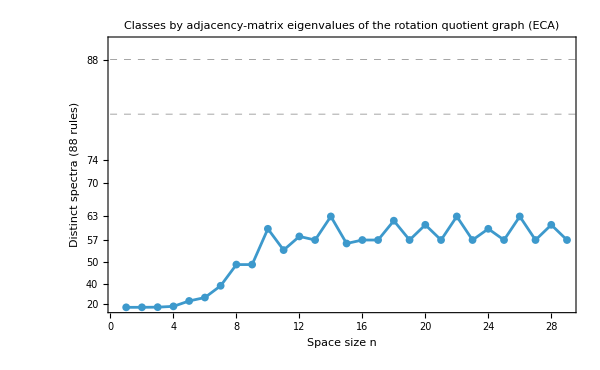

```mathematica
ptsEigRot={#["n"],#["Classes"]}&/@Values[KeySort[eigRotData]];
yScale={#^3&,CubeRoot};
ListLinePlot[ptsEigRot,PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct spectra (88 rules)"},FrameTicks->{{{20,40,50,57,63,70,74,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by adjacency-matrix eigenvalues of the rotation quotient graph (ECA)"]
```

### Gráfica combinada

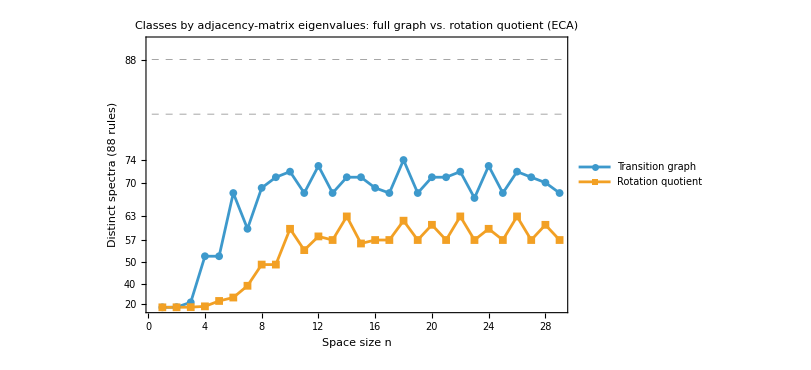

```mathematica
ptsEig={#["n"],#["Classes"]}&/@Values[KeySort[eigData]];
ptsEigRot={#["n"],#["Classes"]}&/@Values[KeySort[eigRotData]];
yScale={#^3&,CubeRoot};
ListLinePlot[{ptsEig,ptsEigRot},PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct spectra (88 rules)"},FrameTicks->{{{20,40,50,57,63,70,74,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[{"Transition graph","Rotation quotient"},{{0.97,0.08},{1,0}}],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by adjacency-matrix eigenvalues: full graph vs. rotation quotient (ECA)"]
```

### Resultados

Clases por n: 3, 5, 8, 14, 26, 30, 39, 49, 49, 60, 54, 58 para n = 1..12. Desde n = 13 los tamaños impares dan siempre 57 (salvo 15, con 56), n ≡ 2 (mod 4) da 62 o 63 y 4 | n da 57, 60 o 61. Siempre son menos que sin cocientar (67–74), y la forma canónica del cociente siempre separa al menos lo mismo que su espectro.

Particiones idénticas: {13, 17, 19, 23, 25, 29}, {14, 22, 26}, {20, 28} y {21, 27}; los demás tamaños quedan aparte. Combinando los 29 tamaños se obtienen 68 clases. En todos los tamaños tienen el mismo espectro {0, 8}, {1, 19}, {2, 24, 36, 46, 72}, {4, 12, 34}, {15, 51}, {18, 126}, {23, 33}, {40, 78}, {42, 76}, {128, 136}, {130, 152}, {132, 140, 162, 168}, {138, 200} y {170, 204}: además de las reglas con los mismos ciclos del grafo completo, el cociente junta las que difieren en componer con el desplazamiento, como {15, 51} y {170, 204}.

Combinando el espectro del grafo completo y el del cociente en el mismo tamaño se obtienen como máximo 77 clases (n = 18), y combinando todo, 77: a diferencia de la forma canónica, el cociente no agrega información a los eigenvalores, porque ninguno de los dos ve los transitorios.

## Momentos espectrales en GPU: 88 reglas, n = 1, …, 29

Clasificación de las 88 reglas representantes por sus momentos espectrales m_k = |{x : F^k(x) = x}|/N, k = 1, …, K, para n = 1, …, 29 células. Misma metodología que las secciones anteriores: una regla por clase de inverso + espejo, un archivo de datos, el resultado iconizado y la gráfica.

m_k depende solo del histograma de ciclos: una configuración cumple F^k(x) = x si y solo si está en un ciclo de longitud L con L | k, así que m_k = (Σ_{L | k} L c_L)/N. Los momentos se calculan en forma exacta (racionales) a partir de los histogramas de la sección de eigenvalores en GPU (eigData); si eigData no está cargado, CyclesFor los calcula con CycleHistogram. Se guardan los vectores con K = 60 y las clases se cuentan comparando los primeros K momentos, con K = 10, 20, 30 y 60.

Validación: para n = 1..8 los primeros 20 momentos de las 88 reglas coinciden con el conteo directo de las configuraciones con F^k(x) = x, iterando la regla en CPU.

### Funciones

```mathematica
(* Momentos espectrales exactos a partir del histograma de ciclos: m_k = (número de configuraciones con F^k(x) = x)/N = suma de L c_L sobre los ciclos con L | k, dividida entre N *)
SpectralMomentsExact[cycles_List,nodes_Integer,K_Integer]:=Table[Total[(#[[1]]#[[2]])&/@Select[cycles,Divisible[k,#[[1]]]&]],{k,K}]/nodes;
(* Histograma de ciclos de una regla: se reutiliza el de eigData (misma GPU) si existe; si no, se calcula con CycleHistogram *)
CyclesFor[r_Integer,n_Integer]:=If[AssociationQ[eigData]&&KeyExistsQ[eigData,n],First[Select[eigData[n]["Rules"],#["Rule"]==r&]]["Cycles"],CycleHistogram[Subscript[r,2,3],n]["Cycles"]];
smKs={10,20,30,60};
```

### Experimento

Cada tamaño se guarda en spectral_moments_gpu_data.wl. Requiere EigenSpectrum/ecaReps/nMax y eigData de la sección de eigenvalores en GPU (o la sección Funciones para recalcular los histogramas).

```mathematica
dataFileSM=FileNameJoin[{Quiet[Check[NotebookDirectory[],Directory[]]],"spectral_moments_gpu_data.wl"}];
smResults=If[FileExistsQ[dataFileSM],Get[dataFileSM],<||>];
Do[If[!KeyExistsQ[smResults,n],Module[{rows,t},t=First[AbsoluteTiming[rows=Table[<|"Rule"->r,"n"->n,"Moments"->SpectralMomentsExact[CyclesFor[r,n],2^n,Max[smKs]]|>,{r,ecaReps}]]];smResults[n]=<|"n"->n,"Seconds"->t,"Classes"->AssociationMap[Function[K,CountDistinct[Take[#,K]&/@rows[[All,"Moments"]]]],smKs],"Groups"->AssociationMap[Function[K,Values[GroupBy[rows,Take[#["Moments"],K]&,#[[All,"Rule"]]&]]],smKs],"Rules"->rows|>;Put[smResults,dataFileSM]]],{n,1,nMax}];
Dataset[<|"n"->#["n"],Sequence@@KeyValueMap[("K = "<>ToString[#1])->#2&,#["Classes"]]|>&/@Values[KeySort[smResults]]]
```

### Datos (Iconize)

```mathematica
smData=;
```

### Gráfica

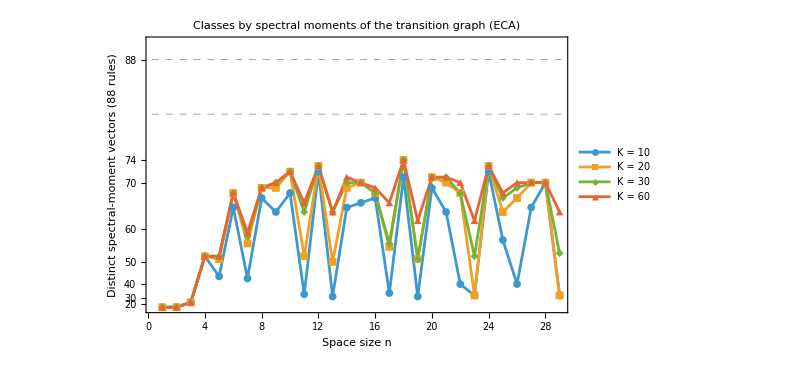

```mathematica
ptsSM=Table[{#["n"],#["Classes"][K]}&/@Values[KeySort[smData]],{K,smKs}];
yScale={#^3&,CubeRoot};
ListLinePlot[ptsSM,PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct spectral-moment vectors (88 rules)"},FrameTicks->{{{20,30,40,50,60,70,74,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[("K = "<>ToString[#])&/@smKs,LegendLayout->"Row"],{{0.5,0.645},{0.5,0.5}}],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by spectral moments of the transition graph (ECA)"]
```

### Resultados

El número de clases depende de la ventana K: un ciclo de longitud L > K nunca aparece en el vector. Con K = 10 (el valor usado en el paper) los tamaños con ciclos largos pierden mucha información: n = 11, 13, 17, 19, 23 y 29 dan entre 31 y 34 clases, y n = 22 y 26 dan 40. Con n compuesto los ciclos cortos dominan y K = 10 ya da entre 64 y 72 clases. El máximo con K = 10 es 72 (n = 12 y 24).

Al crecer K el número de clases se acerca al de los eigenvalores: con K = 60 coincide en 17 de los 29 tamaños, y nunca lo supera, porque los momentos son una función del espectro. Con n ≤ 4 todos los ciclos caben en la ventana y el resultado no depende de K.

Combinando los 29 tamaños se obtienen 77 clases con cualquier K = 10, 20, 30 o 60, igual que con los eigenvalores: siempre tienen el mismo vector {0, 8}, {1, 19}, {2, 24, 46}, {4, 12}, {18, 126}, {36, 72}, {128, 136}, {130, 152}, {132, 140} y {162, 168}. Los momentos heredan la ceguera a los transitorios del espectro.

## Momentos espectrales del cociente por rotaciones: 88 reglas, n = 1, …, 29

Mismos momentos espectrales, pero sobre el grafo cociente por rotaciones: m_k es la fracción de clases de rotación [x] con G^k([x]) = [x], donde G es la función inducida en el cociente. Cada clase cuenta como un nodo y el vector se normaliza por el número de clases (unos 2^n/n). Es la definición que da los 63 vectores distintos con n = 14 y K = 10 que se reportan en el paper (63 también entre las 88 reglas representantes).

Los momentos se calculan en forma exacta a partir de los histogramas de ciclos del cociente de la sección anterior (eigRotData); si no está cargado, CyclesRotFor los calcula con AllocateQuotient y EigenvaluesRotGPU. Igual que sin cocientar, se guardan los vectores con K = 60 y se cuentan las clases con K = 10, 20, 30 y 60.

Validación: para n = 1..8 los primeros 20 momentos de las 88 reglas coinciden con el conteo directo de las clases con G^k([x]) = [x], construyendo el cociente e iterándolo en CPU.

### Funciones

```mathematica
(* Histograma de ciclos del cociente: se reutiliza el de eigRotData (misma GPU) si existe; si no, se calcula con AllocateQuotient y EigenvaluesRotGPU. Cada clase de rotación cuenta como un nodo y se normaliza por el número de clases *)
CyclesRotFor[r_Integer,n_Integer]:=If[AssociationQ[eigRotData]&&KeyExistsQ[eigRotData,n],First[Select[eigRotData[n]["Rules"],#["Rule"]==r&]][[{"Cycles","Nodes"}]],EigenvaluesRotGPU[r,AllocateQuotient[n]][[{"Cycles","Nodes"}]]];
```

### Experimento

Cada tamaño se guarda en spectral_moments_rot_gpu_data.wl. Requiere SpectralMomentsExact y smKs de la sección anterior, y eigRotData de la sección de eigenvalores del cociente (o sus funciones para recalcular los histogramas).

```mathematica
dataFileSMRot=FileNameJoin[{Quiet[Check[NotebookDirectory[],Directory[]]],"spectral_moments_rot_gpu_data.wl"}];
smRotResults=If[FileExistsQ[dataFileSMRot],Get[dataFileSMRot],<||>];
Do[If[!KeyExistsQ[smRotResults,n],Module[{rows,t},t=First[AbsoluteTiming[rows=Table[With[{c=CyclesRotFor[r,n]},<|"Rule"->r,"n"->n,"Nodes"->c["Nodes"],"Moments"->SpectralMomentsExact[c["Cycles"],c["Nodes"],Max[smKs]]|>],{r,ecaReps}]]];smRotResults[n]=<|"n"->n,"Nodes"->rows[[1,"Nodes"]],"Seconds"->t,"Classes"->AssociationMap[Function[K,CountDistinct[Take[#,K]&/@rows[[All,"Moments"]]]],smKs],"Groups"->AssociationMap[Function[K,Values[GroupBy[rows,Take[#["Moments"],K]&,#[[All,"Rule"]]&]]],smKs],"Rules"->rows|>;Put[smRotResults,dataFileSMRot]]],{n,1,nMax}];
Dataset[<|"n"->#["n"],"Nodes"->#["Nodes"],Sequence@@KeyValueMap[("K = "<>ToString[#1])->#2&,#["Classes"]]|>&/@Values[KeySort[smRotResults]]]
```

### Datos (Iconize)

```mathematica
smRotData=;
```

### Gráfica

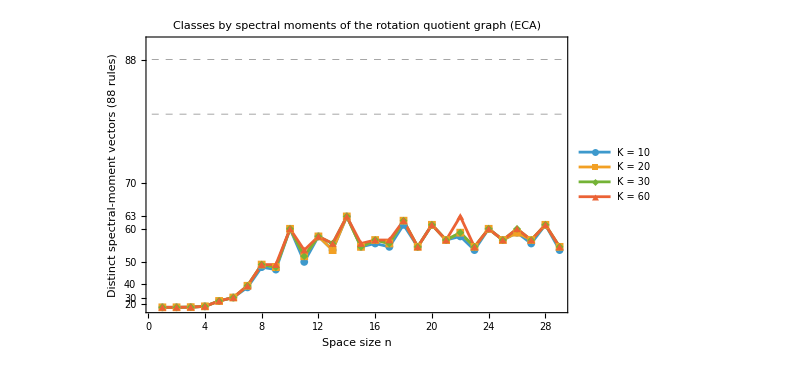

```mathematica
ptsSMRot=Table[{#["n"],#["Classes"][K]}&/@Values[KeySort[smRotData]],{K,smKs}];
yScale={#^3&,CubeRoot};
ListLinePlot[ptsSMRot,PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct spectral-moment vectors (88 rules)"},FrameTicks->{{{20,30,40,50,60,63,70,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[("K = "<>ToString[#])&/@smKs,LegendLayout->"Row"],{{0.5,0.645},{0.5,0.5}}],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by spectral moments of the rotation quotient graph (ECA)"]
```

### Gráfica combinada

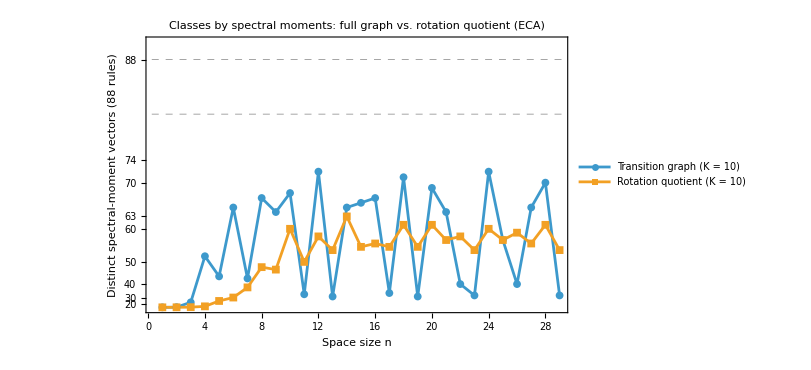

```mathematica
ptsSM10={#["n"],#["Classes"][10]}&/@Values[KeySort[smData]];
ptsSMRot10={#["n"],#["Classes"][10]}&/@Values[KeySort[smRotData]];
yScale={#^3&,CubeRoot};
ListLinePlot[{ptsSM10,ptsSMRot10},PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct spectral-moment vectors (88 rules)"},FrameTicks->{{{20,30,40,50,60,63,70,74,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[{"Transition graph (K = 10)","Rotation quotient (K = 10)"},LegendLayout->"Row"],{{0.5,0.645},{0.5,0.5}}],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by spectral moments: full graph vs. rotation quotient (ECA)"]
```

Gráfica combinada para el paper (Figura fig:sm-classes): las cuatro ventanas K = 10, 20, 30, 60 en el grafo completo (línea continua) y en el cociente (línea punteada). Se exporta a exports/ y a Paper/figures/ como spectral_moments_classes_combined_gpu.png.

```mathematica
dir = Quiet[Check[NotebookDirectory[], Directory[]]];
ks = {10, 20, 30, 60};
kCols = {RGBColor[0.24, 0.6, 0.8], RGBColor[0.95, 0.627, 0.1425], RGBColor[0.455, 0.7, 0.21], RGBColor[0.922526, 0.385626, 0.209179]};
seriesK[d_] := Table[({#["n"], #["Classes"][k]} &) /@ Values[KeySort[d]], {k, ks}];
yScale = {#^3 &, CubeRoot};
refTicks = {{81, Style["81 (4 inheritance)", 15, Gray]}, {88, Style["88 (state permutation, mirror)", 15, Gray]}};
combinedPlot[full_, rot_, yTicks_, title_] := Module[{opts, pFull, pRot, legK, legG},
  opts = Sequence[PlotMarkers -> {Automatic, 9}, Frame -> True, ScalingFunctions -> {None, yScale},
    PlotRange -> {{0, 29.5}, {0, 90}}, GridLines -> {None, {81, 88}}, GridLinesStyle -> Directive[Gray, Dashed],
    FrameLabel -> {"Space size n", "Distinct vectors (88 rules)"}, FrameTicks -> {{yTicks, refTicks}, {Automatic, Automatic}},
    FrameTicksStyle -> 15, LabelStyle -> Directive[Black, 16], AspectRatio -> 0.5, ImageSize -> 900];
  pFull = ListLinePlot[seriesK[full], PlotStyle -> (Directive[#, AbsoluteThickness[2]] & /@ kCols), opts];
  pRot = ListLinePlot[seriesK[rot], PlotStyle -> (Directive[#, AbsoluteThickness[2], AbsoluteDashing[{6, 4}]] & /@ kCols), opts];
  legK = LineLegend[kCols, ("K = " <> ToString[#]) & /@ ks, LegendMarkers -> {Automatic, 11}, LegendLayout -> "Row", LabelStyle -> 17];
  legG = LineLegend[{Directive[Gray, AbsoluteThickness[2]], Directive[Gray, AbsoluteThickness[2], AbsoluteDashing[{6, 4}]]},
    {"Transition graph", "Rotation quotient"}, LegendLayout -> "Row", LabelStyle -> 17, LegendMarkerSize -> {40, 12}];
  Legended[Show[pFull, pRot, PlotLabel -> Style[title, 18]], Placed[Column[{legK, legG}, Alignment -> Center], Below]]];
smCombined = combinedPlot[Get[FileNameJoin[{dir, "spectral_moments_gpu_data.wl"}]], Get[FileNameJoin[{dir, "spectral_moments_rot_gpu_data.wl"}]],
  {20, 40, 50, 60, 70, 74}, "Spectral moments, full graph and rotation quotient (ECA)"];
Export[FileNameJoin[{dir, "exports", "spectral_moments_classes_combined_gpu.png"}], smCombined, ImageResolution -> 150];
Export[FileNameJoin[{dir, "Paper", "figures", "spectral_moments_classes_combined_gpu.png"}], smCombined, ImageResolution -> 150];
smCombined
```

### Resultados

Clases por n con K = 10: 3, 5, 8, 14, 26, 30, 38, 48, 47, 60, 50, 58, 54, 63, 55 para n = 1..15 y entre 54 y 61 para n = 16..29. El máximo es 63, con n = 14.

En el cociente la ventana K importa mucho menos que en el grafo completo: la diferencia entre K = 10 y K = 60 es de a lo más 5 clases (n = 22), y los tamaños primos ya no se desploman. Al cocientar, los ciclos que solo recorren las rotaciones de una configuración (por ejemplo, los de longitud n de los desplazamientos) se vuelven puntos fijos, y los ciclos que quedan son mucho más cortos. Con K = 60 las clases coinciden con las de los eigenvalores del cociente en 24 de los 29 tamaños. Por eso, con K = 10 el cociente distingue más reglas que el grafo completo en n = 11, 13, 17, 19, 22, 23, 26 y 29, justo los tamaños en los que la ventana corta hace que el grafo completo se desplome (gráfica combinada).

Combinando los 29 tamaños se obtienen 68 clases con cualquier K (igual que con los eigenvalores del cociente), y combinando además los momentos del grafo completo, 77 con cualquier K. Con un solo tamaño, los momentos (K = 10) del grafo completo y del cociente juntos dan como máximo 77 clases, con n = 18. Como en los eigenvalores, el cociente no agrega información: los momentos heredan la ceguera a los transitorios.

## Momentos espectrales con masa de atractor en GPU: 88 reglas, n = 1, …, 29

Clasificación de las 88 reglas representantes por los momentos espectrales con masa de atractor (Sección 5.3 del paper), para n = 1, …, 29. Para cada configuración x se usan su altura h(x) (pasos para llegar al ciclo) y el periodo p(x) de su ciclo; x cuenta en el paso k si p(x) | k y h(x) ≤ k − p(x), es decir, desde la activación j0 = 1 + ⌈h/p⌉ de su ciclo. El vector es m~_k = |{x que cuentan en k}|/N, k = 1, …, K.

attractorMassC recorre el arreglo de sucesores (SuccessorArrayGPU) una sola vez en O(N): sigue cada camino hasta un nodo con altura conocida o hasta cerrar un ciclo, asigna periodo y altura hacia atrás y acumula la tabla c[p, j0] para p j0 ≤ 60. Con esa tabla, m~_k es la suma de c[p, j0] con p | k y p j0 ≤ k. Usa tres arreglos de 32 bits de tamaño N (6 GB con n = 29). Se guardan las tablas y los vectores con K = 60, y las clases se cuentan con K = 10, 20, 30 y 60.

Validación: reproduce los tres ejemplos del paper con 5 células (regla 0: (1, 32, 32, …)/32; regla 8: (1, 12, 32, …)/32; regla 30: (1, 2, 2, 2, 7, 2, 2, 2, 2, 32, …)/32), y para n = 1..10 los primeros 30 momentos de las 88 reglas coinciden con el cálculo directo de h(x) y p(x) iterando cada configuración.

### Funciones

```mathematica
(* Altura h y periodo p de cada nodo en un solo recorrido O(N): se sigue cada camino hasta un nodo conocido o hasta cerrar un ciclo y se asignan las alturas hacia atrás. Cada nodo cuenta desde k = p j0 con j0 = 1 + Ceiling[h/p]; se devuelve la tabla c[p, j0] (aplanada) para p j0 <= kmax *)
attractorMassC=FunctionCompile[Function[{Typed[succ,TypeSpecifier["NumericArray"]["Integer32",1]],Typed[kmax,"MachineInteger"]},Module[{n=Length[succ],hgt,per,stack,top=0,w,v,u,h,p,j0,cnt,cstart,len},hgt=CreateTypeInstance[TypeSpecifier["CArray"]["Integer32"],n];per=CreateTypeInstance[TypeSpecifier["CArray"]["Integer32"],n];stack=CreateTypeInstance[TypeSpecifier["CArray"]["Integer32"],n];Do[ToRawPointer[hgt,i0,Cast[-1,"Integer32","CCast"]],{i0,0,n-1}];cnt=ConstantArray[0,kmax*kmax];Do[If[FromRawPointer[hgt,s]==Cast[-1,"Integer32","CCast"],top=0;w=s;While[FromRawPointer[hgt,w]==Cast[-1,"Integer32","CCast"],ToRawPointer[hgt,w,Cast[-2,"Integer32","CCast"]];ToRawPointer[per,w,Cast[top,"Integer32","CCast"]];ToRawPointer[stack,top,Cast[w,"Integer32","CCast"]];top++;w=Cast[succ[[w+1]],"MachineInteger","CCast"]];len=top;If[FromRawPointer[hgt,w]==Cast[-2,"Integer32","CCast"],cstart=Cast[FromRawPointer[per,w],"MachineInteger","CCast"];Do[u=Cast[FromRawPointer[stack,i],"MachineInteger","CCast"];ToRawPointer[hgt,u,Cast[0,"Integer32","CCast"]];ToRawPointer[per,u,Cast[top-cstart,"Integer32","CCast"]],{i,cstart,top-1}];top=cstart];Do[v=Cast[FromRawPointer[stack,i],"MachineInteger","CCast"];u=Cast[succ[[v+1]],"MachineInteger","CCast"];ToRawPointer[hgt,v,FromRawPointer[hgt,u]+Cast[1,"Integer32","CCast"]];ToRawPointer[per,v,FromRawPointer[per,u]],{i,top-1,0,-1}];Do[v=Cast[FromRawPointer[stack,i],"MachineInteger","CCast"];h=Cast[FromRawPointer[hgt,v],"MachineInteger","CCast"];p=Cast[FromRawPointer[per,v],"MachineInteger","CCast"];j0=1+Quotient[h+p-1,p];If[p*j0<=kmax,cnt[[(p-1)*kmax+j0]]++],{i,0,len-1}]],{s,0,n-1}];DeleteObject[hgt];DeleteObject[per];DeleteObject[stack];cnt]]];
(* Vector de momentos con masa de atractor: m~_k = (suma de c[p, j0] con p | k y p j0 <= k)/N *)
AttractorMassMoments[c_List,nodes_Integer,K_Integer]:=Table[Sum[If[Divisible[k,p],Total[c[[p,1;;k/p]]],0],{p,1,k}],{k,K}]/nodes;
amKmax=60;amKs={10,20,30,60};
(* Una regla en el grafo completo: sucesores en GPU y alturas en CPU compilado *)
AttractorMassGPU[r_Integer,n_Integer]:=Module[{c=Partition[attractorMassC[SuccessorArrayGPU[Subscript[r,2,3],n],amKmax],amKmax]},<|"Rule"->r,"n"->n,"Nodes"->2^n,"Counts"->c,"Moments"->AttractorMassMoments[c,2^n,amKmax]|>];
```

### Experimento

Cada tamaño se guarda en attractor_mass_gpu_data.wl. Requiere la sección Funciones (sesión CUDA, SuccessorArrayGPU) y ecaReps/nMax de la sección de eigenvalores en GPU. Tiempo total: unos 40 min (n = 29 tarda 21 min; el recorrido es en CPU).

```mathematica
dataFileAM=FileNameJoin[{Quiet[Check[NotebookDirectory[],Directory[]]],"attractor_mass_gpu_data.wl"}];
amResults=If[FileExistsQ[dataFileAM],Get[dataFileAM],<||>];
Do[If[!KeyExistsQ[amResults,n],Module[{rows,t},t=First[AbsoluteTiming[rows=Table[AttractorMassGPU[r,n],{r,ecaReps}]]];amResults[n]=<|"n"->n,"Seconds"->t,"Classes"->AssociationMap[Function[K,CountDistinct[Take[#,K]&/@rows[[All,"Moments"]]]],amKs],"Groups"->AssociationMap[Function[K,Values[GroupBy[rows,Take[#["Moments"],K]&,#[[All,"Rule"]]&]]],amKs],"Rules"->rows|>;Put[amResults,dataFileAM]]],{n,1,nMax}];
Dataset[<|"n"->#["n"],Sequence@@KeyValueMap[("K = "<>ToString[#1])->#2&,#["Classes"]]|>&/@Values[KeySort[amResults]]]
```

### Datos (Iconize)

```mathematica
amData=;
```

### Gráfica

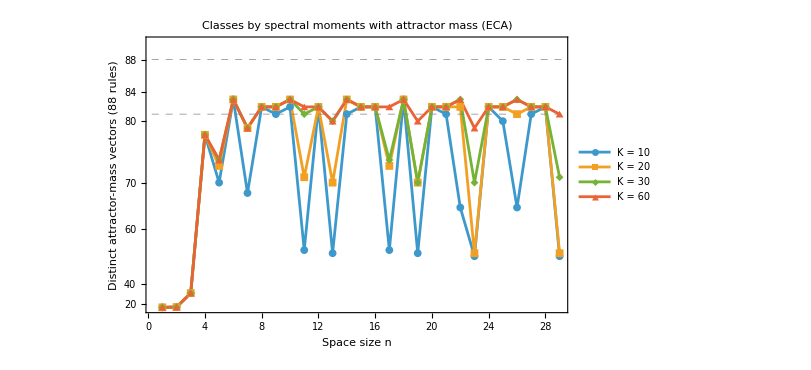

```mathematica
ptsAM=Table[{#["n"],#["Classes"][K]}&/@Values[KeySort[amData]],{K,amKs}];
yScale={#^3&,CubeRoot};
ListLinePlot[ptsAM,PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct attractor-mass vectors (88 rules)"},FrameTicks->{{{20,40,60,70,80,84,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[("K = "<>ToString[#])&/@amKs,LegendLayout->{"Row",2}],Below],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by spectral moments with attractor mass (ECA)"]
```

### Resultados

Clases por n con K = 10: 3, 9, 34, 78, 70, 83, 68, 82, 81, 82 para n = 1..10. Desde ahí, los tamaños con divisores chicos dan entre 80 y 83 clases, muy por encima de los momentos espectrales (máximo 72 con K = 10) y de los eigenvalores (máximo 74). El máximo es 83, con n = 6 y 18 (y con n = 10, 14, 22 y 26 si K ≥ 20 o 30). Nunca supera a la forma canónica (82–85 clases): dos grafos isomorfos dan el mismo vector, y en todos los tamaños la partición por forma canónica es más fina.

Como en los momentos espectrales, con K = 10 los tamaños con ciclos largos pierden información (n = 11, 13, 17, 19, 23, 29 dan entre 52 y 54 clases; n = 22 y 26 dan 65). Al subir K se recuperan: con K = 60, n = 29 da 81 y n = 23 da 79.

Las reglas 0 y 8 quedan separadas para todo n ≥ 3. Combinando los 29 tamaños se obtienen 86 clases con cualquier K (contra 77 de eigenvalores y momentos espectrales), y dos tamaños chicos ya bastan: por ejemplo n = 1 y 6, o n = 3 y 6. Solo quedan juntos dos pares: {1, 19}, cuyas alturas exactas difieren (con p = 2, h = 1 contra h = 2) pero caen en el mismo intervalo de p pasos, que es la limitación de resolución del método; y {4, 12}, que tienen exactamente la misma distribución de (p, h) y solo difieren en la forma de los árboles.

## Momentos espectrales con masa de atractor del cociente por rotaciones: 88 reglas, n = 1, …, 29

Mismos momentos con masa de atractor, pero sobre el grafo cociente por rotaciones: h y p se calculan sobre el cociente, cada clase de rotación cuenta como un nodo y el vector se normaliza por el número de clases (la misma convención que los momentos espectrales del cociente). Los sucesores del cociente se calculan en GPU con AllocateQuotient y kSuccQuot, y attractorMassC recorre solo los unos 2^n/n nodos: las 88 reglas con n = 29 tardan 43 s.

Validación: para n = 1..8 los primeros 30 momentos coinciden con el cálculo directo de h y p sobre el cociente construido en CPU. En todos los tamaños la partición por forma canónica del cociente es más fina que la de este vector.

Nota: AllocateQuotient recorta succ a exactamente nr entradas. La primera versión usaba ZerosInt32[nr], que redondea la longitud hacia arriba; con n ≥ 25 (nr > 2^20) quedaban nodos de sobra apuntando al nodo 0. Eso no cambia los ciclos (los eigenvalores y momentos del cociente se verificaron idénticos para n = 21..29), pero sí las alturas, así que la masa de atractor se recalculó para n = 21..29 con la versión corregida.

### Funciones

```mathematica
(* Una regla en el cociente por rotaciones: sucesores del cociente en GPU (kSuccQuot) y alturas en CPU compilado; cada clase cuenta como un nodo *)
AttractorMassRotGPU[r_Integer,buf_Association]:=Module[{c},kSuccQuot[buf["succ"],buf["reps"],buf["idx"],r,buf["n"],buf["total"],buf["N"],"GridDimensions"->Quotient[buf["N"]-1,256]+1,"BlockDimensions"->256];c=Partition[attractorMassC[NumericArray[buf["succ"]],amKmax],amKmax];<|"Rule"->r,"n"->buf["n"],"Nodes"->buf["N"],"Counts"->c,"Moments"->AttractorMassMoments[c,buf["N"],amKmax]|>];
```

### Experimento

Cada tamaño se guarda en attractor_mass_rot_gpu_data.wl. Requiere attractorMassC, AttractorMassMoments, amKmax/amKs de la sección anterior y AllocateQuotient/kSuccQuot de la sección de eigenvalores del cociente.

```mathematica
dataFileAMRot=FileNameJoin[{Quiet[Check[NotebookDirectory[],Directory[]]],"attractor_mass_rot_gpu_data.wl"}];
amRotResults=If[FileExistsQ[dataFileAMRot],Get[dataFileAMRot],<||>];
Do[If[!KeyExistsQ[amRotResults,n],Module[{buf=AllocateQuotient[n],rows,t},t=First[AbsoluteTiming[rows=Table[AttractorMassRotGPU[r,buf],{r,ecaReps}]]];amRotResults[n]=<|"n"->n,"Nodes"->buf["N"],"Seconds"->t,"Classes"->AssociationMap[Function[K,CountDistinct[Take[#,K]&/@rows[[All,"Moments"]]]],amKs],"Groups"->AssociationMap[Function[K,Values[GroupBy[rows,Take[#["Moments"],K]&,#[[All,"Rule"]]&]]],amKs],"Rules"->rows|>;Put[amRotResults,dataFileAMRot]]],{n,1,nMax}];
Dataset[<|"n"->#["n"],"Nodes"->#["Nodes"],Sequence@@KeyValueMap[("K = "<>ToString[#1])->#2&,#["Classes"]]|>&/@Values[KeySort[amRotResults]]]
```

### Datos (Iconize)

```mathematica
amRotData=;
```

### Gráfica

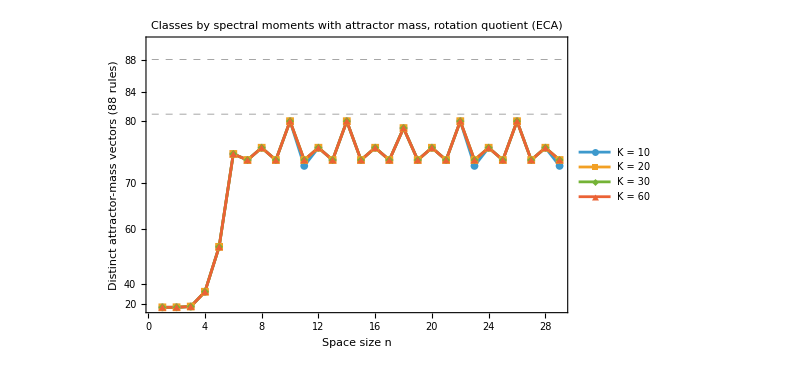

```mathematica
ptsAMRot=Table[{#["n"],#["Classes"][K]}&/@Values[KeySort[amRotData]],{K,amKs}];
yScale={#^3&,CubeRoot};
ListLinePlot[ptsAMRot,PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct attractor-mass vectors (88 rules)"},FrameTicks->{{{20,40,60,70,80,84,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[("K = "<>ToString[#])&/@amKs,LegendLayout->{"Row",2}],Below],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by spectral moments with attractor mass, rotation quotient (ECA)"]
```

### Gráfica combinada

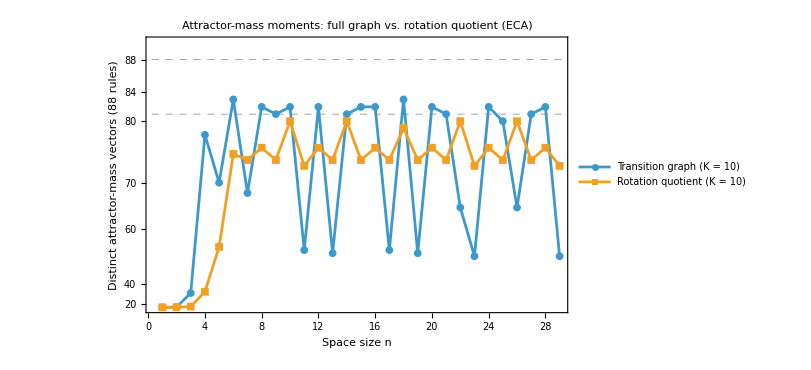

```mathematica
ptsAM10={#["n"],#["Classes"][10]}&/@Values[KeySort[amData]];
ptsAMRot10={#["n"],#["Classes"][10]}&/@Values[KeySort[amRotData]];
yScale={#^3&,CubeRoot};
ListLinePlot[{ptsAM10,ptsAMRot10},PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct attractor-mass vectors (88 rules)"},FrameTicks->{{{20,40,60,70,80,84,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[{"Transition graph (K = 10)","Rotation quotient (K = 10)"},LegendLayout->{"Row",2}],Below],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Attractor-mass moments: full graph vs. rotation quotient (ECA)"]
```

Gráfica combinada para el paper (Figura fig:am-classes): las cuatro ventanas K = 10, 20, 30, 60 en el grafo completo (línea continua) y en el cociente (línea punteada). Se exporta a exports/ y a Paper/figures/ como attractor_mass_classes_combined_gpu.png.

```mathematica
dir = Quiet[Check[NotebookDirectory[], Directory[]]];
ks = {10, 20, 30, 60};
kCols = {RGBColor[0.24, 0.6, 0.8], RGBColor[0.95, 0.627, 0.1425], RGBColor[0.455, 0.7, 0.21], RGBColor[0.922526, 0.385626, 0.209179]};
seriesK[d_] := Table[({#["n"], #["Classes"][k]} &) /@ Values[KeySort[d]], {k, ks}];
yScale = {#^3 &, CubeRoot};
refTicks = {{81, Style["81 (4 inheritance)", 15, Gray]}, {88, Style["88 (state permutation, mirror)", 15, Gray]}};
combinedPlot[full_, rot_, yTicks_, title_] := Module[{opts, pFull, pRot, legK, legG},
  opts = Sequence[PlotMarkers -> {Automatic, 9}, Frame -> True, ScalingFunctions -> {None, yScale},
    PlotRange -> {{0, 29.5}, {0, 90}}, GridLines -> {None, {81, 88}}, GridLinesStyle -> Directive[Gray, Dashed],
    FrameLabel -> {"Space size n", "Distinct vectors (88 rules)"}, FrameTicks -> {{yTicks, refTicks}, {Automatic, Automatic}},
    FrameTicksStyle -> 15, LabelStyle -> Directive[Black, 16], AspectRatio -> 0.5, ImageSize -> 900];
  pFull = ListLinePlot[seriesK[full], PlotStyle -> (Directive[#, AbsoluteThickness[2]] & /@ kCols), opts];
  pRot = ListLinePlot[seriesK[rot], PlotStyle -> (Directive[#, AbsoluteThickness[2], AbsoluteDashing[{6, 4}]] & /@ kCols), opts];
  legK = LineLegend[kCols, ("K = " <> ToString[#]) & /@ ks, LegendMarkers -> {Automatic, 11}, LegendLayout -> "Row", LabelStyle -> 17];
  legG = LineLegend[{Directive[Gray, AbsoluteThickness[2]], Directive[Gray, AbsoluteThickness[2], AbsoluteDashing[{6, 4}]]},
    {"Transition graph", "Rotation quotient"}, LegendLayout -> "Row", LabelStyle -> 17, LegendMarkerSize -> {40, 12}];
  Legended[Show[pFull, pRot, PlotLabel -> Style[title, 18]], Placed[Column[{legK, legG}, Alignment -> Center], Below]]];
amCombined = combinedPlot[Get[FileNameJoin[{dir, "attractor_mass_gpu_data.wl"}]], Get[FileNameJoin[{dir, "attractor_mass_rot_gpu_data.wl"}]],
  {20, 40, 60, 70, 74, 80, 84}, "Attractor mass, full graph and rotation quotient (ECA)"];
Export[FileNameJoin[{dir, "exports", "attractor_mass_classes_combined_gpu.png"}], amCombined, ImageResolution -> 150];
Export[FileNameJoin[{dir, "Paper", "figures", "attractor_mass_classes_combined_gpu.png"}], amCombined, ImageResolution -> 150];
amCombined
```

### Resultados

Clases por n: 3, 6, 13, 35, 55, 75 para n = 1..6. Desde n = 7, con K = 60, el número depende solo de n mod 4: 74 si n es impar, 80 si n ≡ 2 (mod 4) (79 con n = 18) y 76 si 4 | n; con K = 10 algunos impares bajan a 73. Las particiones son idénticas dentro de cada familia: impares 7–29, {8, 16, 20, 28}, {10, 14, 22, 26}, {12, 24} y {18}. En el cociente la ventana casi no importa (los ciclos del cociente son cortos).

Combinando los 29 tamaños el cociente da 81 clases con cualquier K. Siempre quedan juntos {4, 12, 34}, {15, 51}, {42, 76}, {132, 162}, {138, 200} y {170, 204}: el cociente identifica cada regla con su composición con la traslación (15 = ¬l y 51 = ¬c, 170 = r y 204 = c, 12 = ¬l ∧ c y 34 = ¬c ∧ r), igual que en la forma canónica del cociente.

Combinando el grafo completo y el cociente en el mismo tamaño se obtienen 87 clases con n = 6, 10, 12, 14, 18, 22, 24 y 26 (86 con n = 8, 16, 20, 28), y combinando todo, 87 con cualquier K. El único par que ningún tamaño ni ninguna de las dos versiones separa es {4, 12}: tienen exactamente la misma distribución de altura y periodo, y solo la forma canónica los distingue. Es decir, la masa de atractor recupera casi toda la información de la forma canónica (que da 88 con n = 6 y ambos grafos), pero con un vector de longitud fija K que sirve para comparar dominios distintos.

### Comparación de los métodos

Gráficas comparativas: número de clases de los cuatro métodos (forma canónica, eigenvalores, momentos espectrales y masa de atractor, K = 10) en el grafo completo y en el cociente.

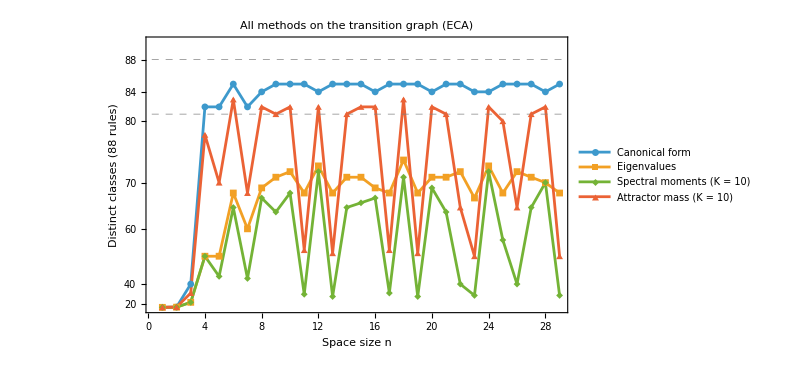

```mathematica
dir=Quiet[Check[NotebookDirectory[],Directory[]]];
ld[f_]:=Get[FileNameJoin[{dir,f}]];
series={{#["n"],#["Classes"]}&/@Values[KeySort[ld["canonical_form_gpu_data.wl"]]],{#["n"],#["Classes"]}&/@Values[KeySort[ld["eigenvalues_gpu_data.wl"]]],{#["n"],#["Classes"][10]}&/@Values[KeySort[ld["spectral_moments_gpu_data.wl"]]],{#["n"],#["Classes"][10]}&/@Values[KeySort[ld["attractor_mass_gpu_data.wl"]]]};
yScale={#^3&,CubeRoot};
ListLinePlot[series,PlotMarkers->{Automatic,7},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct classes (88 rules)"},FrameTicks->{{{20,40,60,70,80,84,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[{"Canonical form","Eigenvalues","Spectral moments (K = 10)","Attractor mass (K = 10)"},LegendLayout->{"Row",2}],Below],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"All methods on the transition graph (ECA)"]
```

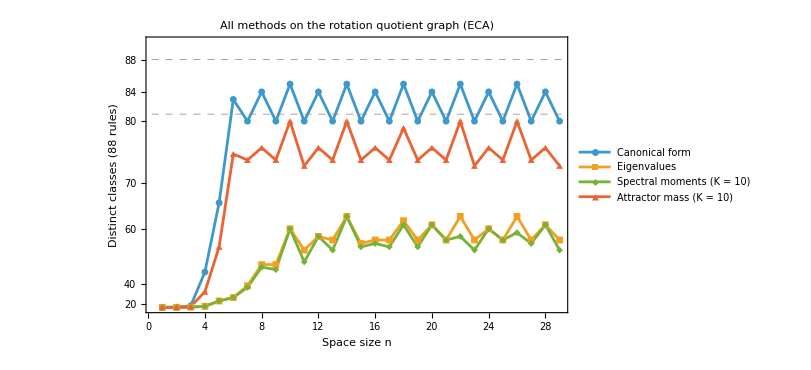

```mathematica
dir=Quiet[Check[NotebookDirectory[],Directory[]]];
ld[f_]:=Get[FileNameJoin[{dir,f}]];
seriesRot={{#["n"],#["Classes"]}&/@Values[KeySort[ld["canonical_form_rot_gpu_data.wl"]]],{#["n"],#["Classes"]}&/@Values[KeySort[ld["eigenvalues_rot_gpu_data.wl"]]],{#["n"],#["Classes"][10]}&/@Values[KeySort[ld["spectral_moments_rot_gpu_data.wl"]]],{#["n"],#["Classes"][10]}&/@Values[KeySort[ld["attractor_mass_rot_gpu_data.wl"]]]};
yScale={#^3&,CubeRoot};
ListLinePlot[seriesRot,PlotMarkers->{Automatic,7},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct classes (88 rules)"},FrameTicks->{{{20,40,60,70,80,84,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[{"Canonical form","Eigenvalues","Spectral moments (K = 10)","Attractor mass (K = 10)"},LegendLayout->{"Row",2}],Below],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"All methods on the rotation quotient graph (ECA)"]
```